# Machine Learning

## Part 1: Introduction

Yen Lee Loh, 2022-12-6

Stuff to set up
– Anaconda (with Jupyter Lab): install and configure (tab stops, hotkeys, etc.)
– PyTorch (follow instructions to install WITH CUDA support)
– Your directory structure!

Topics to be covered in this series of Mathematica and Jupyter notebooks
– What is machine learning?
– Unsupervised learning
	– Principal Component Analysis (PCA)
	– Non-negative Matrix Factorization (NMF)
– Supervised learning
	– Generalized Linear Models, linear regression, logistic regression
	– Support Vector Classification
	– (Feedforward) (Artificial) Neural Networks
		– Single-Layer Perceptron
		– Multi-Layer Perceptron
		– Convolutional Neural Networks
	– The PyTorch framework:
		        Types of neural network layers
		        Automatic differentiation
		        Optimizers
		        1D curve fitting using NNs
		        Multidimensional function fitting using NNs
		        Image recognition: homemade images/MNIST/CIFAR
		        Using GPUs (CUDA)
		        Microphone audio and webcam images

## Section What is Machine Learning?

Machine learning tasks can usually be categorized as supervised learning or unsupervised learning, as described below.

### Section.Subsection Unsupervised learning

Unsupervised learning involves unlabeled data sets.  A typical workflow is as follows.

1.  Choose a training dataset that consists of training data x_n^train.
2.  Find a model function Y(x) that converts the input x into some kind of output Y.
3.  Choose a test dataset consisting of test data x_n^test.
4.  Apply the model function to the test data.

Below are some examples of unsupervised learning methods and applications.

Associative memory using a Hopfield network
– We are given a set of binary images {x_nij^train}.
– Consider an Ising model on lattice.  The couplings {J_ij} are small and random.
– Train the network using Hebbian learning (“neurons that fire together wire together”): in each image, if two pixels are similar, increment J_ij, else decrement
– Given a partial image {x_ij^test}, find a local or global minimum of the energy of the Ising model; this may allow the network to reconstruct (recall) the image from partial data.

Clustering
– We are given a set of points {x_n^train}.
– Identify clusters of points such that all points within the same cluster have ||x_m-x_n||<R_1 whereas any pair of points from different clusters have ||x_m-x_n||>R_2
– Construct a model function Y(x) that returns the cluster index (an integer) corresponding to the point x 
– Given a test point x_n^test, we may apply Y(x) to determine which cluster it belongs to (or if it does not belong to any of the previously identified clusters)
Examples:
	– given many images of galaxies, ask the computer to automatically “sort” them into different “categories”, WITHOUT supervision

Dimensional reduction
– We are given a set of points {x_n^train}
– We wish to identify “similarities” and “differences” within the dataset 
– For example, if all the points lie in the xy plane, then the z coordinate carries no information
– If the points all have similar x values but the y values differ a lot, then we are more interested in the y values
– Basically, we want to know which features of the dataset have the most variance
– One can do this using principal component analysis

### Section.Subsection Supervised learning

https://en.wikipedia.org/wiki/Supervised_learning
Supervised learning (SL) is the machine learning task of learning a function that maps an input to an output based on example input-output pairs.  It infers a function from labeled training data consisting of a set of training examples.  In supervised learning, each example is a pair consisting of an input object (typically a vector) and a desired output value (also called the supervisory signal).  A supervised learning algorithm analyzes the training data and produces an inferred function, which can be used for mapping new examples.  An optimal scenario will allow for the algorithm to correctly determine the class labels for unseen instances. This requires the learning algorithm to generalize from the training data to unseen situations in a “reasonable” way (see inductive bias). This statistical quality of an algorithm is measured through the so-called generalization error.

A typical workflow for supervised learning is as follows.

1.  Choose a training dataset that consists of training inputs x_n^train and training outputs y_n^train.  (Usually x is a vector and y is a scalar.)

2.  Choose a type of machine (generalized linear model, support vector machine, neural network, decision tree, etc.).  A machine is described by its model output function Y(x|w) and model output probability distribution P(y|x,w), where w are learnable model parameters.

3.  Train a machine to learn the input-output relation.  For machines with deterministic outputs, this means finding values of the parameters w that maximize the probability for the outputs to be obtained from the inputs, P({y_n^train}|{x_n^train},w).  For machines with probabilistic outputs Y_n^train, one may wish to find w to minimize the Kullback-Leibler divergence between P(Y_n^train|x,w) and P(y_n^train|x), defined as D_KL(P_data||P_model)=∑_y P_data(y)ln (P_data(y))/(P_model(y)).

4.  Evaluate ∑_n f(Y_n^train,y_n^train), which is a measure of goodness-of-fit –– the ability to recall the correct outputs for inputs that the model has seen.
5.  Choose a test dataset consisting of test inputs x_n^test and test outputs y_n^test.
6.  Evaluate ∑_n f(Y_n^test,y_n^test), which is a measure of generalization ability –  whether the model is able to predict outputs for inputs that it has not seen before.
7.  We are now ready to apply our model to a real-world data set x_n^rw for which we do not know the outputs.  For each data point x, we may use the model in several ways:
	a.  Predict the probability distribution of the output, P(y|x).
	b.  Predict the mean value of the output, Y(x)≡⟨y⟩.
	c.  Predict the most likely output, Y_ml(x)=argmax P(y|x).
	d.  Generate a random output from P(y|x).

Below are some examples of supervised learning applications.

Binary classification

	Input | Output | Example 
input | Model output
probabilities | Most likely 
output
Binary vector | Binary value | {0,0,0}
{1,0,1} | 0.01
0.99 | 0
1
Real vector | Binary value | {7,6,4}
{1,2,3} | 0.00
1.00 | DOWNWARD_TREND
UPWARD_TREND
Character vector | Binary value | HELLO
BONJOUR |   | ENGLISH
FRENCH
Grayscale image | Binary value | -Graphics-
 |   | EVEN_DIGIT
ODD_DIGIT
RGB image | Binary value | 
 |   | SPIRAL_GALAXY


ELLIPTICAL_GALAXY

k-way classification
– In principle, this can be reduced to multiple binary classification problems.

Prediction (deterministic)
	Energy of 1D Ising model:
	Binary vector ⟶ numeric value		{↑,↑,↑}⟶-2.0			{↑,↓,↑}⟶+2.0
	Energy of 1D chain of atoms in terms of displacements:
	Numeric vector ⟶ numeric value		{+1,+2,+1}⟶3.0		{+1,-2,+1}⟶18.0
Generation
	Binary vector ⟶ binary vector		{0,0,0}⟶{0,1,0} generated from some probability dist P(y|x) e.g., using RBM

#### details

(Details on item 3:)


	Usually, this means maximizing the likelihood of w given {y_n^train}.
	This is equivalent to minimizing a loss/cost/penalty/objective/negative-log-likelihood function.  
	The cost is usually of the form F(w)=∑_n f(Y_n^train,y_n^train).
	Here Y_n^train=Y(x_n^train) are the predicted outputs based on training outputs and F(Y_n,y_n) is a measure of distance.

	In the case of RBMs it’s a bit more complicated.  The RBM generates a probabilistic output Y_n^train,
	and we want to minimize the Kullback-Leibler divergence between P(Y_n^train|x,w) and P(y_n^train|x),
		D_KL(P_data||P_model)=∑_y P_data(y)ln (P_data(y))/(P_model(y)).

### Section.Subsection Feature extraction

Preprocessing
Often, the raw input vector x=(x_1,x_2,…,x_D) in a machine learning problem is not in a form suitable for direct application of the above ML techniques.  Some processing is recommended.  Real-valued inputs should be scaled.  Images should be centered and rotated appropriately (if possible), so that the machine doesn’t end up comparing apples to oranges.  Real-valued outputs may also need to be scaled: a MLP generates an output in the range [-1,1], so we need to map this range to the range of training outputs (e.g., [503 eV,517 eV] in a materials science application).

Manual feature extraction
More sophisticated preprocessing may be useful.  One may transform the input vector x into a feature vector u=(u_1,u_2,…,u_N_feat).  The components of this vector are feature values.  The number of feature values, N_feat, may be equal to, greater than, or less than the size of the input vector.  We can do manual feature extraction.  For example, for handwriting recognition for 8×8 binary images, one might attempt to use features such as:

– size and aspect ratio of of bounding box of ON pixels
– 0th, 1st, 2nd, 3rd, 4th moments of “mass” about center of bounding box 
	(e.g., “8” is the digit with the greatest total mass; the numeral “1” is slender and tall; “3” is heavy at the right)
– topological genus (“1,2,3,5,7” have genus 0, “0,6,9” have genus 1, “8” has genus 4); may be misleading because a lot of people don’t write carefully
– Fourier components (“3”, “5”, “8” have relatively large number of horizontal stripes)

Automatic feature extraction
Instead of manually defining feature extraction functions, one may use unsupervised learning techniques to do automatic feature extraction (even if the overall task involves supervised learning).  For example:

– do a principal component analysis on Fourier components of images, to see what kind of features vary in a most prominent way
   (e.g., if we were classifying horses versus zebras, we expect that zebras have high-frequency Fourier components)
– do a principal component analysis on average image color in (R,G,B) or (H,S,V) color spaces
– clustering analysis of male and female faces without giving training labels (machine might automatically assign classes such as “has moustache” and “has no moustache”, which human might not think of if coding manual feature extraction)

### Section.Subsection Various thoughts (TBD)

Artificial Intelligence (AI)
	- Human-programmed approaches
	- Machine Learning (ML)
		- Supervised Learning
			-(Artificial) Neural Networks (NN or ANN)
			-Convolutional Neural Networks (CNNs), RNNs, etc.
		- Unsupervised Learning
			- some other kinds of networks

Applications.

Curve fitting
Learning from data for period of pendulum (say) and then predicting period for new situations
Predictive texting
Image recognition: Faces, fingerprints, computer vision, handwriting-to-text, 
Voice recognition: voice-to-text, interpret
Weather forecasting?  Can this use AI as opposed to traditional weather/climate modeling?
Forecasting of all sorts: given some time series data {x_1,x_2,…,x_1000}, predict x_1001?

#### I think Mathematica does a PCA in the simplest cases.... or even not as good as a PCA

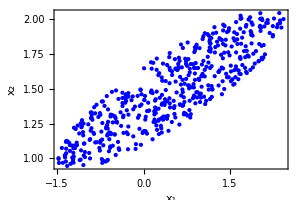
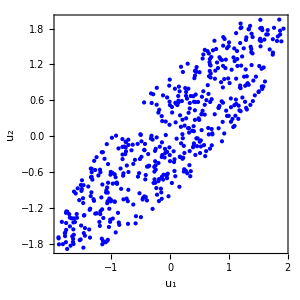

```mathematica
genRandom2Vec[]:=Module[{x1,x2},
While[True,
{x1,x2}=RandomReal[{-2,2},2];
If[x1^2-6x1 x2+12 x2^2<1^2&&ArcTan[x1,x2]<2.9,Return[{x1,x2}+{.5,1.5}]];
];
];
xn=Table[genRandom2Vec[],500];
fe=FeatureExtraction[xn];
un=fe/@xn;
Row@{
Graphics[{Blue,Point/@xn},Frame->True,PlotRange->3,ImageSize->300,FrameLabel->{"x_1","x_2"}],
Graphics[{Blue,Point/@un},Frame->True,PlotRange->3,ImageSize->300,FrameLabel->{"u_1","u_2"}]
}
```

The top left panel shows 500 input vectors in a dataset.
The top right panel shows the resulting 500 feature vectors generated by Mathematica’s FeatureExtraction[].  The coordinates appear to have been scaled and shifted, but Mathematica hasn’t even attempted to do a rotation (which PCA would do).

## Section Examples

Titanic dataset

```mathematica
data=ExampleData[{"MachineLearning","Titanic"},"Data"];
x1=data⟦All,1,1⟧;
x2=data⟦All,1,2⟧;
x3=data⟦All,1,3⟧;
y=data⟦All,2⟧;
TableForm[{x1,x2,x3,y}ᵀ⟦1;;10⟧,TableHeadings->{None,{"Cabin class","Age","Gender","Result"}}]
```

Cabin class | Age | Gender | Result
1st | 29. | female | survived
1st | 0.9167 | male | survived
1st | 2. | female | died
1st | 30. | male | died
1st | 25. | female | died
1st | 48. | male | survived
1st | 63. | female | survived
1st | 39. | male | died
1st | 53. | female | survived
1st | 71. | male | died

```mathematica
data=ExampleData[{"MachineLearning","Titanic"},"Data"];
x1=data⟦All,1,1⟧/.{"1st"->1,"2nd"->2,"3rd"->3};
x2=data⟦All,1,2⟧//Round;
x3=data⟦All,1,3⟧/.{"female"->0,"male"->1};
y=data⟦All,2⟧/.{"died"->0,"survived"->1};
TableForm[{x1,x2,x3,y}ᵀ⟦1;;10⟧,TableHeadings->{None,{"Class","Age","Sex","Result"}}]
```

Class | Age | Sex | Result
1 | 29 | 0 | 1
1 | 1 | 1 | 1
1 | 2 | 0 | 0
1 | 30 | 1 | 0
1 | 25 | 0 | 0
1 | 48 | 1 | 1
1 | 63 | 0 | 1
1 | 39 | 1 | 0
1 | 53 | 0 | 1
1 | 71 | 1 | 0

## Initialization cells

### Section.Subsection Basics

```mathematica
Solid=Dashing@{};
DarkGreen=Darker[Green,0.67];
resistorColorList={Black,Brown,Red,Orange,Darker@Yellow,Darker@Green,Blue,Purple,Gray,Cyan};
resistorStyle[n_Integer]:={AbsoluteThickness@1,resistorColorList[[Mod[n,Length@resistorColorList,1]]]};
purpleWhite[v_]:=Hue[0.75,0.25,Abs[v]^0.5];
blueWhiteRed[v_]:=Hue[If[v>0.5,0.0,0.5],(2Abs[v-0.5]),0.95];
colorFromComplex[z_,OptionsPattern[{Brightness->1.}]]:=Hue[Rescale[Arg@z,{0,2 π}],0.8,1-1/(1+Abs[z*OptionValue[Brightness]])];
enlargeFont=#/.s_String->Style[s,16]&;
myCF=Blend[{
Hue[0.8,0.75,0.75],
Hue[0.7,0.75,0.80],
Hue[0.6,0.75,0.90],
Hue[0.6,0.25,1.00],
White,
RGBColor[0.9938925000000001,0.989345,0.5766145],
RGBColor[0.955963,0.863115,0.283425],
RGBColor[0.881316,0.5539655,0.2226795],
RGBColor[0.817319,0.134167,0.164218]},
Clip[#,{0,1}]]&;
myCF=Blend[{
Hue[0.67,0.75,0.80],
White,
Hue[.15,.75,.80]},
Clip[#,{0,1}]]&;
```

```mathematica
myGS={BaseStyle->{14,FontFamily->"Times",Black}};
myPS={LabelStyle->{14,FontFamily->"Times",Black},ImageSize->324,RotateLabel->False,Frame->True,FrameStyle->Directive@{AbsoluteThickness@0,Black},ImageMargins->1};
myPS1={PlotStyle->ColorData[97]};
SetOptions[Graphics,myGS];
SetOptions[Plot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ParametricPlot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ListPlot,myGS,myPS,myPS1];
SetOptions[ListLinePlot,myGS,myPS,myPS1];
SetOptions[ListLogPlot,myGS,myPS];
SetOptions[ListLogLogPlot,myGS,myPS];
SetOptions[ListLogLinearPlot,myGS,myPS];
SetOptions[DiscretePlot,myGS,myPS];
SetOptions[RectangleChart,myGS,myPS];
SetOptions[ArrayPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[ContourPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[DensityPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[StreamPlot,myGS,myPS,AspectRatio->Automatic,StreamColorFunction->None,StreamStyle->AbsoluteThickness@1];
SetOptions[Graphics3D,PlotRange->All,ImageSize->600,ViewPoint->{-1,-2,1},ViewVertical->{0,0,1},Lighting->"Neutral",Boxed->False,AspectRatio->Automatic];
```

### Section.Subsection Dimension lines (relatively new code: 2021-2-16)

```mathematica
(*---- USER MAY WANT TO TWEAK ARROWSIZE ----*)
dimLine[r1_,r2_,label_,tickLen_,arrowOffset_,labelOffset_]:=Module[{p,u,v,w,
arrowSize=0.015,
grAH=
Graphics[Line@{{-1,.3},{0,0},{-1,-.3}}]
(*Graphics[Polygon@{{-1,.5},{0,0},{-1,-.5}}]*)
},
p=r2-r1;u=Normalize@{-p⟦2⟧,p⟦1⟧};p=Normalize@p;
(*-------- CHECK IF DIMENSION IS SUFFICIENTLY LARGE --------*)
If[
Norm[r2-r1]>.8    (*5Max[tickLen,arrowOffset,labelOffset]*)
,
(*-------- ORDINARY INTERIOR DIMENSION LINE --------*)
{
Arrowheads[{{-arrowSize,Automatic,grAH},{arrowSize,Automatic,grAH}}],Arrow@{r1+arrowOffset*u,r2+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
},
(*-------- SPECIAL EXTERIOR DIMENSION LINE --------*)
{
exteriorLength=1;
Arrowheads[{{arrowSize,Automatic,grAH}}],
Arrow@{r2+exteriorLength*p+arrowOffset*u,r2+arrowOffset*u},
Arrow@{r1-exteriorLength*p+arrowOffset*u,r1+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
}
]
];
groundSymbol[{x_,y_},s_]:=(
Line@{{{0,3},{0,6}},{{-3,3},{3,3}},{{-2,2},{2,2}},{{-1,1},{1,1}}}
)//Translate[#,{0,-6}]&//Scale[#,s,{0,0}]&//Translate[#,{x,y}]&;
```

### Section.Subsection myFormat

```mathematica
(*-------- Pretty-print any real number --------*)
myFormat[v_]:=(
Which[
(*---- If v is an exact power of 10 with an exponent less than -4 or greater than +4, display v as 10^w ----*)
v>0&&Abs@Log10@v>5&&FractionalPart[Log10@v]==0,SuperscriptBox[10,Round@Log10@v],
(*---- If v is an integer, display v without any decimal points ----*)
Abs[v-Round@v]<10^-8,Round@v,
(*---- If v is not an integer, display v with decimals and possibly in scientific notation ----*)
True,NumberForm[N@v,ExponentFunction->(If[-4<#<4,Null,#]&),NumberPoint->"."]
](*//Style[#,FontWeight->Bold]&*));
```

### Section.Subsection Axis utilities: divisions, etc.

Let v be the numerical part of a physical quantity, and let x be the coordinate along the axis on which this quantity is plotted.
For example, suppose we are displaying 200 GHz at coordinate 8.3.  Then v=200×10^11 and x=8.3.
We will supply a conversion function vfromx to the myAxis function.

```mathematica
(*-------- Plotting parameters --------*)
maxMajorDivisions=30;
maxMinorDivisions=300;
tickLengthMajorP=0.25;
tickLengthMajorM=0.;
tickLengthMinorP=0.15;
tickLengthMinorM=0.;
textOffset=1.5;
(*-------- Round up or down to closest number in a list --------*)
roundUp[x_,xlist_]:=Min@Select[xlist,#≥x&];
roundDn[x_,xlist_]:=Max@Select[xlist,#≤x&];
(*-------- Round up or down to the nearest number of the form 1×10^n, 2×10^n, or 5×10^n --------*)
roundUpNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundUp[x/10^expon,{1,2,5,10}]*10^expon];
roundDnNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundDn[x/10^expon,{1,2,5,10}]*10^expon];
(*-------- Divide an interval to find a nice set of tick values --------*)
divisions[{vmin_,vmax_},maxDivisions_]:=Module[{vrange,vstep,vstart,lmin,lmax,v,divs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxDivisions];
vstart=vstep*Ceiling[vmin/vstep];
divs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
Return@divs;
];
(*-------- Divide an interval to find nice major and minor tick values --------*)
divisions[{vmin_,vmax_},{maxMajorDivisions_,maxMinorDivisions_}]:=Module[{vrange,vstep,vstart,lmin,lmax,v,majDivs,minDivs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxMajorDivisions]; (* major division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
majDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
vstep=roundUpNicely[vstep/maxMinorDivisions]; (* minor division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
minDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
minDivs=Complement[minDivs,majDivs];
Return@{majDivs,minDivs}];
(*-------- Divide an interval with major ticks as 10^n and minor ticks as {2,3,4,5,6,7,8,9}×10^n --------*)
(*-------- This works well except when we have a very small interva --------*)
logDivisions[{vmin_,vmax_}]:=Module[{lmin,lmax,v,majDivs,minDivs}, (* l===Log10[v] *)
lmin=Floor@Log10@vmin;
lmax=Ceiling@Log10@vmax;
majDivs=Table[v=10^l;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax}]//Reap//Last//Last;
minDivs=Table[v=10^l*mantissa;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax},{mantissa,2,9}]//Reap//Last//Last;
Return@{majDivs,minDivs}];
linScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=divisions[{vmin,vmax},{30,6}];
vlist2=Flatten@vlist2;
Graphics[{
(*-------- Draw axis line and axis label --------*)
Text[label,{xmin,0},{2.00,0}],
{Line@{{xmin,0},{xmax,0}}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
logScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=Quiet@InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=myLogDivisions[{vmin,vmax}];vlist2=Flatten@vlist2;
(*-------- Draw axis line and axis label --------*)
Graphics[{
Text[label,{xmin,0},{2.00,0}],
Line@{{xmin,0},{xmax,0}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,N@vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
mark[x_,label_]:=Module[{},
{Line@{{x,-10},{x,-.5}},
Text[label,{x,-.5}]}
];
 stackScales[grList_]:=Module[{nmax=Length@grList},
Graphics[{
Table[
(*Inset[grList⟦n⟧,{0,-n}]*)
Translate[grList⟦n⟧⟦1⟧,{0,-n}]
,{n,nmax}],
},
ImageSize->{1200,50*nmax},AspectRatio->Full,
PlotRange->{All,{-nmax-.7,-.1}}
]
]
makeLabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=myFormat},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
makeUnlabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=Null&},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
```

### Section.Subsection autoTicksLabeled, etc.

```mathematica
decimalExponent[x_]:=Floor@Log10[x];
decimalMantissa[x_]:=x/(10^Floor@Log10[x]);
roundUpNicely[x_]:=SelectFirst[{1,2,5,10},#≥decimalMantissa[x]&]*10^decimalExponent[x];
divisions[{xmin_,xmax_},xstep_]:=Range[Ceiling[xmin,xstep],xmax,xstep]//Select[#,xmin≤#≤xmax&]&;
```

```mathematica
autoTicks$TickColor=White; (* MAY NEED TO SET THIS THING *)
autoTicksLabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,myFormat@N@#,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoTicksUnlabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoContours=Function[{zmin,zmax},FindDivisions[{zmin,zmax},50]];
```

### Section.Subsection timeIt

```mathematica
SetAttributes[timeIt,HoldAll];
timeIt[cmds_]:=Module[{report,absTime,cpuTime},
report=AbsoluteTiming[Timing[cmds;]];
absTime=report⟦1⟧;
cpuTime=report⟦2,1⟧;
Print[StringForm["Absolute time = ``    CPU time = ``",absTime//DecimalForm[#,3]&,cpuTime//DecimalForm[#,3]&]]
];
```

### Section.Subsection myRealPlot and myComplexPlot

```mathematica
myRealPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

```mathematica
myComplexPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```